```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
rawdata = Import["DataForPlotting\\SI_SensorBound_data.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{27520,2}

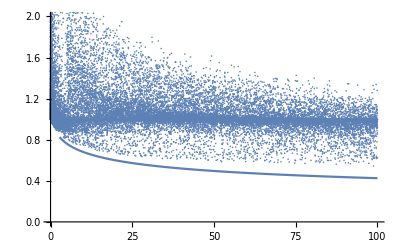

```mathematica
Show[ListPlot[rawdata,PlotRange->{{0,100},{0,2}}],Plot[Sqrt[2/(1+Sqrt[1+x])],{x,0,100}]]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.04}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2/100,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.163908,1.48436}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,25000}];
```

```mathematica
Dimensions[densADJ]
```

{1328,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*100/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

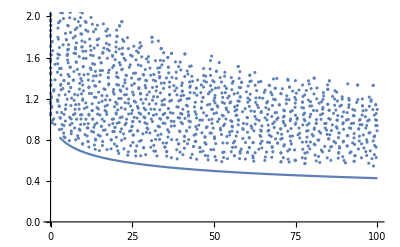

```mathematica
Show[ListPlot[densADJrescaled,PlotRange->{{0,100},{0,2}}],Plot[Sqrt[2/(1+Sqrt[1+x])],{x,0,100}]]
```

```mathematica
Export["DataForPlotting\\SI_SensorBound_densADJ.txt",densADJrescaled, "Table"]
```